```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample/EXTRA_UPSAMPLE"];
meamFiles={"TI_EpotminusEperf_all2_EXTRA","TI_EpotminusEperf_all_EXTRA"};
dftUPFiles={"TI_UP_E0all_EXTRA","TI_UP_Fall_EXTRA"};
meamData=Table[ReadList[meamFiles[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,2}];
dftUPData=Table[ReadList[dftUPFiles[[i]],{Number}],{i,1,2}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols={4.685,4.730,4.759,4.801,4.850};
eVcel2meVatom=1000/64;
```

```mathematica
meam=Partition[Transpose[meamData[[2]]][[5]],101];dft=eVcel2meVatom*Table[Partition[Transpose[dftUPData[[1]]][[1]],101][[i]]-Partition[Transpose[dftUPData[[1]]][[1]],101][[i]][[1]],{i,1,5}];
dftf=eVcel2meVatom*Table[Partition[Transpose[dftUPData[[2]]][[1]],101][[i]]-Partition[Transpose[dftUPData[[2]]][[1]],101][[i]][[1]],{i,1,5}];
```

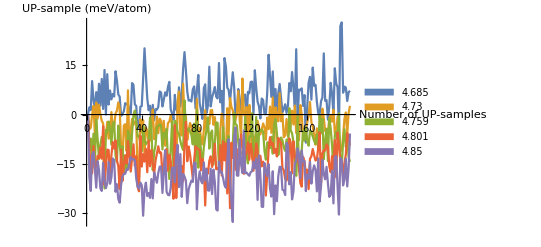

5.76573 | 5.46524 | 0.395451
-3.3491 | 4.8797 | 0.353082
-7.97472 | 4.97612 | 0.360059
-13.6102 | 4.79704 | 0.347101
-18.7258 | 5.39468 | 0.390345

```mathematica
ListLinePlot[Table[(dftf-meam)[[i]],{i,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample (meV/atom)"}]
Table[{Mean[(dftf-meam)[[i]]],StandardDeviation[(dftf-meam)[[i]]],StandardDeviation[(dftf-meam)[[i]]]/Sqrt[Length[(dftf-meam)[[i]]]]},{i,1,5}]//TableForm
```

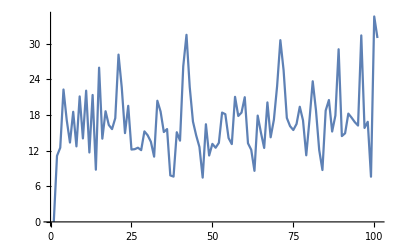

16.8126

5.81228

```mathematica
ListLinePlot@(dft-meam)[[1]]
Mean[(dft-meam)[[1]]]
StandardDeviation[(dft-meam)[[1]]]
```

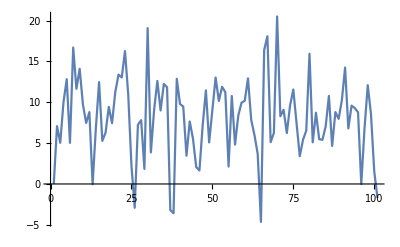

8.04053

4.86792

```mathematica
ListLinePlot@(dft-meam)[[2]]
Mean[(dft-meam)[[2]]]
StandardDeviation[(dft-meam)[[2]]]
```

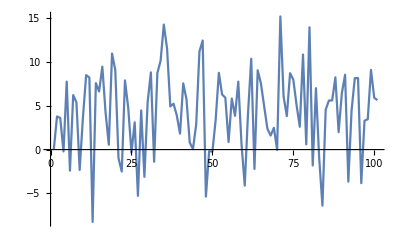

4.27946

4.78484

```mathematica
ListLinePlot@(dft-meam)[[3]]
Mean[(dft-meam)[[3]]]
StandardDeviation[(dft-meam)[[3]]]
```

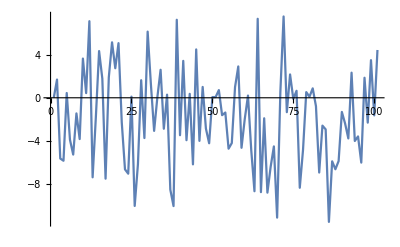

-1.82849

4.38815

```mathematica
ListLinePlot@(dft-meam)[[4]]
Mean[(dft-meam)[[4]]]
StandardDeviation[(dft-meam)[[4]]]
```

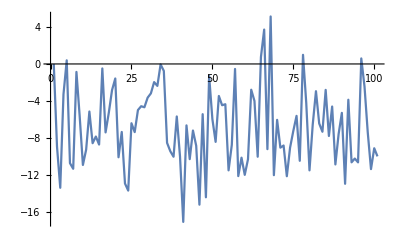

-6.82566

4.32503

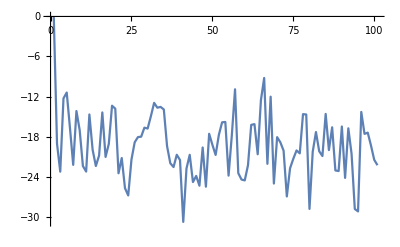

-19.3801

4.80835

```mathematica
ListLinePlot@(dft-meam)[[5]]
Mean[(dft-meam)[[5]]]
StandardDeviation[(dft-meam)[[5]]]
ListLinePlot@(dftf-meam)[[5]]
Mean[(dftf-meam)[[5]]]
StandardDeviation[(dftf-meam)[[5]]]
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
filesEinsteinPot={"T_dudl_meam_4685","T_dudl_meam_4730","T_dudl_meam_4759","T_dudl_meam_4801","T_dudl_meam_4850"};
TdUdL=Table[ReadList[filesEinsteinPot[[i]],{Number, Number}],{i,1,5}];
```

{{-3.81143,-7.54809,-12.686,-14.8639,-18.7054,-23.3822},{-2.32337,-4.48527,-5.97792,-6.51571,-8.18144,-10.4777},{-1.37785,-2.47588,-1.59493,-1.06442,-0.948908,-2.61856},{-0.0762672,0.385152,4.43411,6.89367,8.35227,8.841},{1.23554,3.44112,11.6014,15.7243,19.5159,22.7188}}

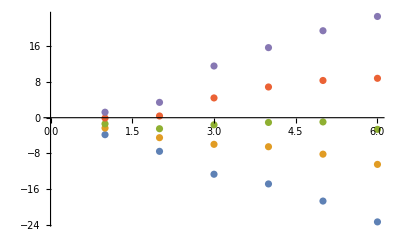

```mathematica
FahData=Integrate[Table[Table[Fit[Partition[TdUdL[[vol]],11][[temp]],{1,x,x^2,x^3,x^4},x],{temp,1,6}],{vol,1,5}],{x,0,1}]
ListPlot@FahData
```

```mathematica
Fah3805=Table[FahData[[i]][[5]],{i,1,5}]
UP3805=Table[Mean[(dft-meam)[[i]]],{i,1,5}]
SD3805=Table[StandardDeviation[(dft-meam)[[i]]],{i,1,5}]
```

{-18.7054,-8.18144,-0.948908,8.35227,19.5159}

{16.8126,8.04053,4.27946,-1.82849,-6.82566}

{5.81228,4.86792,4.78484,4.38815,4.32503}

```mathematica
Fah3805+UP3805
```

{-1.89284,-0.140913,3.33055,6.52379,12.6902}